## Slow roll background

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}},
 endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-60==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

```mathematica
μ:=20
M :=0.005359077192041455(*Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"][[μ,2]];*)
p:=4
ϕini =11.838012784632001;
ϕend=19.328683873439395;
V[p_,t_]:= M^4(1 - (ϕ[t]/μ)^p)
Vp[p_,t_] = D[V[p,t],ϕ[t]];
ten = 4.57 10^6;
sol=NDSolve[{ 3 a'[t]/a[t] ϕ'[t]+Vp[p,t]==0,
a'[t]==a[t]Sqrt[1/3 (V[p,t])], 
ϕ[0]==ϕini,a[0]==1},{ϕ,a},
{t,0,ten},MaxSteps->10000000,AccuracyGoal->10];
ϕsr1[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr1[t],{t,1}];
asr[t_]:= (a/.First[sol])[t]
tend=t/.FindRoot[ϕsr1[t]==ϕend,{t,ten }]; 
tend
ϕend
ϕini
```

FindRoot::nlnum: The function value {-19.3287+InterpolatingFunction[{{0.,4.57×10^6}},{5,3,1,{685},{4},0,0,0,0,Automatic,«3»},{{0.,«9»,«675»}},{{11.838+0. ⅈ,7.3423×10^-7+0. ⅈ},{11.838+0. ⅈ,7.34232×10^-7+0. ⅈ},{11.838+0. ⅈ,7.34233×10^-7+0. ⅈ},«5»,{11.8404+0. ⅈ,7.34715×10^-7+0. ⅈ},{11.841+0. ⅈ,7.34837×10^-7+0. ⅈ},«675»},{Automatic}][«1»]} is not a list of numbers with dimensions {1} at {t} = {4.28907×10^6-109786. ⅈ}.

4.57×10^6

19.3287

11.838

```mathematica
M
```

0.00535908

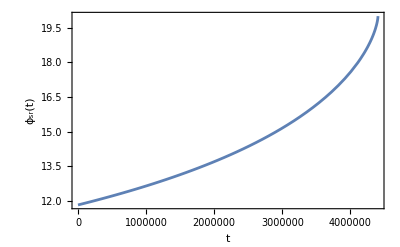

```mathematica
pltphisr = Plot[{ϕsr1[t]}, {t,0,tend}, Frame->True, FrameLabel->{"t", "ϕ_sr(t)"},PlotRange->All,BaseStyle->{FontFamily->"Times",FontSize->15}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\phisrsvstime.pdf", pltphisr,"PDF"]
```

C:\Users\RAUL\Documents\phisrsvstime.pdf

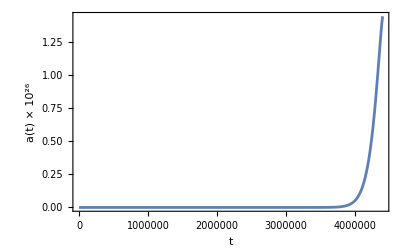

```mathematica
pltasr = Plot[{asr[t]*10^(-
26)}, {t,0,tend}, Frame->True, FrameLabel->{"t", "a(t) × 10^26"},BaseStyle->{FontFamily->"Times",FontSize->15},PlotRange->All]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\asrsvstime.pdf", pltasr,"PDF"]
```

C:\Users\RAUL\Documents\asrsvstime.pdf

## Numerical Background

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}},
 endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-60==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

```mathematica
μ:=20
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"][[μ,2]];
p:=4
ϕend:=First[cend[p,μ]]
ϕini:=First[cini[p,μ]]
V[t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[t_]=D[V[t],ϕ[t]];
ten := 4.57 10^6
(*ϕsr,asr*)
sol=NDSolve[{ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (V[t])], 
ϕ[0]==ϕini,a[0]==1},{ϕ,a},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
asr[t_]:= (a/.First[sol])[t];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,ten *0.9}]; 
tendsr=t/.FindRoot[ϕsr[t]==ϕend,{t,ten *0.8}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {11.838} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

InterpolatingFunction::dmval: Input value {4.74077×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
tend
tendsr
```

4.43099×10^6

4.35531×10^6+0. ⅈ

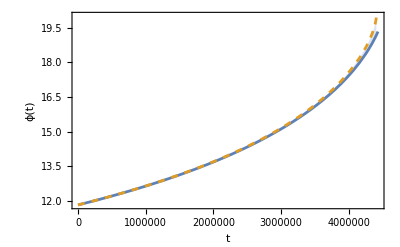

```mathematica
pltphi = Plot[{ϕ[t], ϕsr[t]}, {t,0,tend}, Frame->True, FrameLabel->{"t", "ϕ(t)"},PlotRange->All,BaseStyle->{FontFamily->"Times",FontSize->15},Filling->{1->{2}},PlotStyle->{_,Dashed}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\phivstime.pdf", pltphi,"PDF"]
```

C:\Users\RAUL\Documents\phivstime.pdf

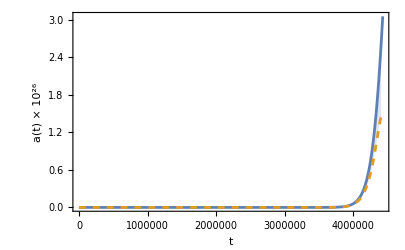

```mathematica
plta= Plot[{a[t]*10^(-
26), asr[t]*10^(-
26)}, {t,0,tend},Frame->True, FrameLabel->{"t", "a(t) × 10^26"},BaseStyle->{FontFamily->"Times",FontSize->15},PlotRange->All,Filling->{1->{2}},PlotStyle->{_,Dashed}]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\avstime.pdf", plta,"PDF"]
```

C:\Users\RAUL\Documents\avstime.pdf